SymbolDependencyGraph

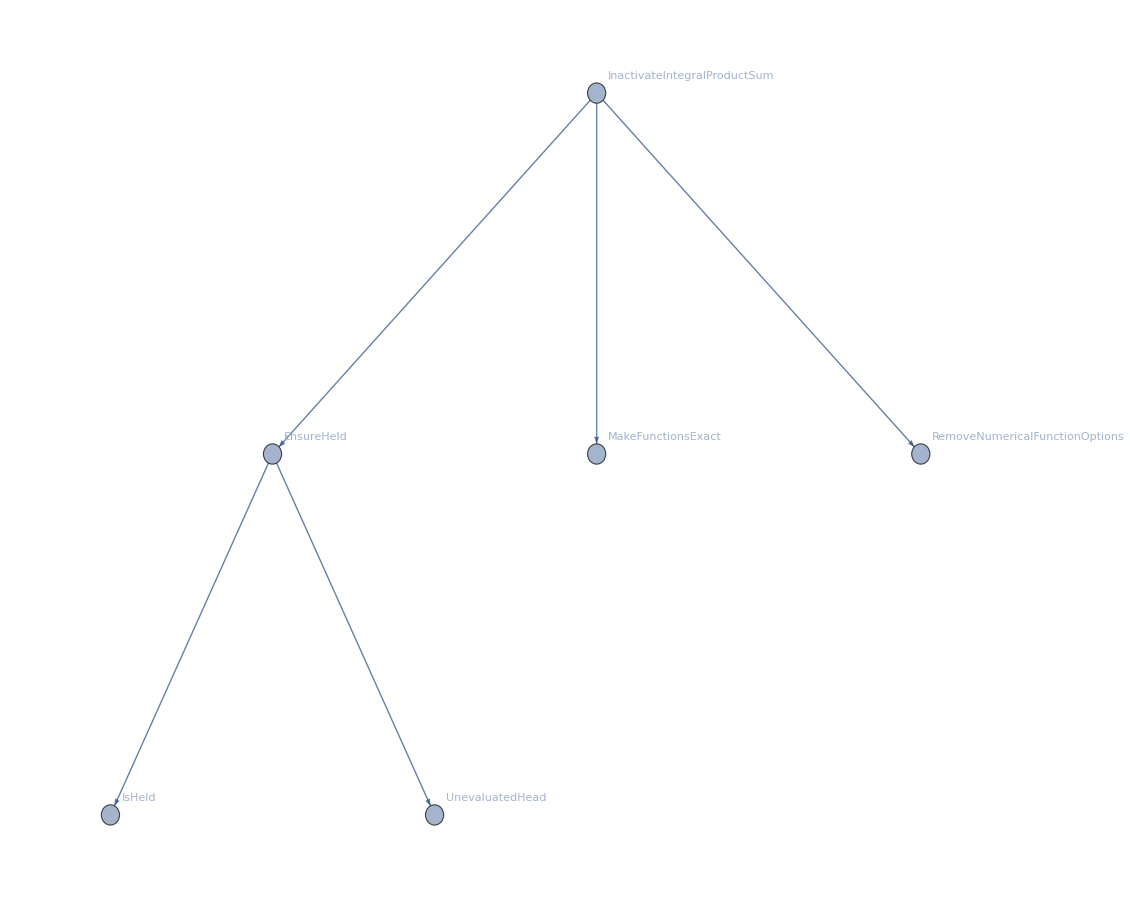

```mathematica
ResourceFunction["SymbolDependencyGraph"][InactivateIntegralProductSum,VertexLabels->Automatic]
```

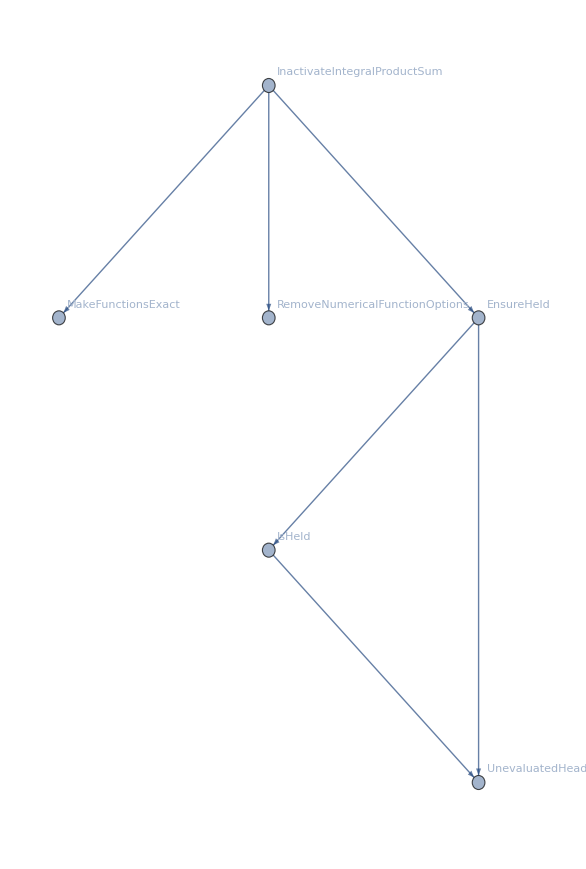
```mathematica
ReverseGraph[-Graphics-]
```

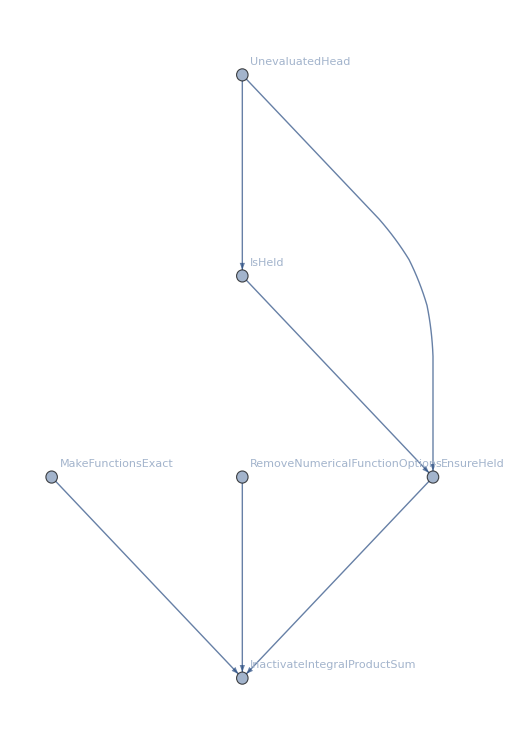

```mathematica
CloudGet["equation1"]
```

W65[a,b,c,d,q,z]==(QPhI[{q,(b^2 c^2 d^2 z^2)/(a^2 q^2),a q,(a q)^(3/2)/(b c d)},q] (q^(1/2 (-1+j) j) (-(a f q)/d)^j QPh[{(a^(3/2) q^(3/2))/(b c)},q,2 j] QPh[{(a^(3/2) √q)/(b c),(√(a q))/b,(√(a q))/c,(a q)/(b c),d},q,j] QPhI[{(f q^(3/4+j/2) √(a^(3/2)/(b c d z)) ρ)/g,(q^(1/4-j/2) √((b c d z)/a^(3/2)) ρ)/(f g),(f g q^(3/4+j/2) √(a^(3/2)/(b c d z)))/ρ,(g q^(1/4-j/2) √((b c d z)/a^(3/2)))/(f ρ),(g q^(1/4+j/2) √((√a b c z)/d))/ρ,(g q^(-1/4+j/2) (b c d z)^(3/2))/(a^(5/4) ρ),(g q^(3/4+(3 j)/2) √((a^(3/2) d z)/(b c)))/ρ},q]/QPhI[{(q^(3/4+j/2) √(a^(3/2)/(b c d z)) ρ)/g,(q^(-3/4-j/2) √((b c d z)/a^(3/2)) ρ)/g,(g q^(1/4+j/2) √(b c d z))/(a^(1/4) ρ),(g q^(-1/4+j/2) √(b c d z))/(a^(1/4) ρ),-(g q^(-1/4+j/2) √(b c d z))/(a^(1/4) ρ),-(g q^(1/4+j/2) √(b c d z))/(a^(1/4) ρ),(g q^(3/4+j/2) √((a^(3/2) z)/(b c d)))/ρ},q]ζ-ππ)/(QPh[{(a^(3/2) √q)/(b c)},q,2 j] QPh[{q,(a q)/b,(a q)/c,√(a q),(a q)^(3/2)/(b c d)},q,j])j0∞)/(2 π QPhI[{f,q/f,(f (a q)^(3/2))/(b c d z),(b c d q z)/(f (a q)^(3/2)),(b^2 c^2 d^2 z^2)/(a^2 q),(a q)/d,(a^(3/2) q^(3/2))/(b c)},q])

```mathematica
EquationQ[CloudGet["equation1"]]
```

False

```mathematica
EquationQ[2+2==4]
```

True

```mathematica
EquationQ[W65[a,b,c,d,q,z]==(QPhI[{q,(b^2 c^2 d^2 z^2)/(a^2 q^2),a q,(a q)^(3/2)/(b c d)},q] (q^(1/2 (-1+j) j) (-(a f q)/d)^j QPh[{(a^(3/2) q^(3/2))/(b c)},q,2 j] QPh[{(a^(3/2) √q)/(b c),(√(a q))/b,(√(a q))/c,(a q)/(b c),d},q,j] QPhI[{(f q^(3/4+j/2) √(a^(3/2)/(b c d z)) ρ)/g,(q^(1/4-j/2) √((b c d z)/a^(3/2)) ρ)/(f g),(f g q^(3/4+j/2) √(a^(3/2)/(b c d z)))/ρ,(g q^(1/4-j/2) √((b c d z)/a^(3/2)))/(f ρ),(g q^(1/4+j/2) √((√a b c z)/d))/ρ,(g q^(-1/4+j/2) (b c d z)^(3/2))/(a^(5/4) ρ),(g q^(3/4+(3 j)/2) √((a^(3/2) d z)/(b c)))/ρ},q]/QPhI[{(q^(3/4+j/2) √(a^(3/2)/(b c d z)) ρ)/g,(q^(-3/4-j/2) √((b c d z)/a^(3/2)) ρ)/g,(g q^(1/4+j/2) √(b c d z))/(a^(1/4) ρ),(g q^(-1/4+j/2) √(b c d z))/(a^(1/4) ρ),-(g q^(-1/4+j/2) √(b c d z))/(a^(1/4) ρ),-(g q^(1/4+j/2) √(b c d z))/(a^(1/4) ρ),(g q^(3/4+j/2) √((a^(3/2) z)/(b c d)))/ρ},q]ζ-ππ)/(QPh[{(a^(3/2) √q)/(b c)},q,2 j] QPh[{q,(a q)/b,(a q)/c,√(a q),(a q)^(3/2)/(b c d)},q,j])j0∞)/(2 π QPhI[{f,q/f,(f (a q)^(3/2))/(b c d z),(b c d q z)/(f (a q)^(3/2)),(b^2 c^2 d^2 z^2)/(a^2 q),(a q)/d,(a^(3/2) q^(3/2))/(b c)},q])]
```

True

```mathematica
Needs["PeterBurbery`BasicHypergeometricFunctions`"]
```

```mathematica
Definition[EquationQ]
```

Attributes[EquationQ]={HoldAll}
 
EquationQ[PeterBurbery`BasicHypergeometricFunctions`Private`b_]:=UnevaluatedHead[PeterBurbery`BasicHypergeometricFunctions`Private`b]===Equal
 
EquationQ[PeterBurbery`BasicHypergeometricFunctions`Private`args___]:=Null/;CheckArguments[EquationQ[PeterBurbery`BasicHypergeometricFunctions`Private`args],1]

```mathematica
?ApplySides
```

```mathematica
ApplySides[f,CloudGet["equation1"]]
```

f[W65[a,b,c,d,q,z]]==f[(QPhI[{q,(b^2 c^2 d^2 z^2)/(a^2 q^2),a q,(a q)^(3/2)/(b c d)},q] (q^(1/2 (-1+j) j) (-(a f q)/d)^j QPh[{(a^(3/2) q^(3/2))/(b c)},q,2 j] QPh[{(a^(3/2) √q)/(b c),(√(a q))/b,(√(a q))/c,(a q)/(b c),d},q,j] QPhI[{(f q^(3/4+j/2) √(a^(3/2)/(b c d z)) ρ)/g,(q^(1/4-j/2) √((b c d z)/a^(3/2)) ρ)/(f g),(f g q^(3/4+j/2) √(a^(3/2)/(b c d z)))/ρ,(g q^(1/4-j/2) √((b c d z)/a^(3/2)))/(f ρ),(g q^(1/4+j/2) √((√a b c z)/d))/ρ,(g q^(-1/4+j/2) (b c d z)^(3/2))/(a^(5/4) ρ),(g q^(3/4+(3 j)/2) √((a^(3/2) d z)/(b c)))/ρ},q]/QPhI[{(q^(3/4+j/2) √(a^(3/2)/(b c d z)) ρ)/g,(q^(-3/4-j/2) √((b c d z)/a^(3/2)) ρ)/g,(g q^(1/4+j/2) √(b c d z))/(a^(1/4) ρ),(g q^(-1/4+j/2) √(b c d z))/(a^(1/4) ρ),-(g q^(-1/4+j/2) √(b c d z))/(a^(1/4) ρ),-(g q^(1/4+j/2) √(b c d z))/(a^(1/4) ρ),(g q^(3/4+j/2) √((a^(3/2) z)/(b c d)))/ρ},q]ζ-ππ)/(QPh[{(a^(3/2) √q)/(b c)},q,2 j] QPh[{q,(a q)/b,(a q)/c,√(a q),(a q)^(3/2)/(b c d)},q,j])j0∞)/(2 π QPhI[{f,q/f,(f (a q)^(3/2))/(b c d z),(b c d q z)/(f (a q)^(3/2)),(b^2 c^2 d^2 z^2)/(a^2 q),(a q)/d,(a^(3/2) q^(3/2))/(b c)},q])]

```mathematica
ApplySides[RearrangeMultiplicativeSubexpressions//@#&,CloudGet["equation1"]]
```

W65[a,b,c,d,q,z]==(QPhI[{q,(b^2**c^2**d^2**z^2)/(q^2**a^2),q**a,(q**a)^(3/2)/(b**c**d)},q]**1/QPhI[{f,q/f,((q**a)^(3/2)**f)/(b**c**d**z),(q**b**c**d**z)/((q**a)^(3/2)**f),(b^2**c^2**d^2**z^2)/(q**a^2),(q**a)/d,(q^(3/2)**a^(3/2))/(b**c)},q])/(2 π)**q^(1/2 (-1+j)**j)**(-(q**a**f)/d)^j**QPh[{(q^(3/2)**a^(3/2))/(b**c)},q,2 j]**QPh[{(√q**a^(3/2))/(b**c),(√(q**a))/b,(√(q**a))/c,(q**a)/(b**c),d},q,j]**QPhI[{(q^(3/4+j/2)**f**ρ**√(a^(3/2)/(b**c**d**z)))/g,(q^(1/4-j/2)**ρ**√((b**c**d**z)/a^(3/2)))/(f**g),(q^(3/4+j/2)**f**g**√(a^(3/2)/(b**c**d**z)))/ρ,(q^(1/4-j/2)**g**√((b**c**d**z)/a^(3/2)))/(f**ρ),(q^(1/4+j/2)**g**√((√a**b**c**z)/d))/ρ,(q^(-1/4+j/2)**g**(b**c**d**z)^(3/2))/(a^(5/4)**ρ),(q^(3/4+(3 j)/2)**g**√((a^(3/2)**d**z)/(b**c)))/ρ},q]/QPhI[{(q^(3/4+j/2)**ρ**√(a^(3/2)/(b**c**d**z)))/g,q^(-3/4-j/2)**1/g**√((b**c**d**z)/a^(3/2))**ρ,(q^(1/4+j/2)**g**√(b**c**d**z))/(a^(1/4)**ρ),(q^(-1/4+j/2)**g**√(b**c**d**z))/(a^(1/4)**ρ),-(q^(-1/4+j/2)**g**√(b**c**d**z))/(a^(1/4)**ρ),-(q^(1/4+j/2)**g**√(b**c**d**z))/(a^(1/4)**ρ),(q^(3/4+j/2)**g**√((a^(3/2)**z)/(b**c**d)))/ρ},q]ζ-ππ/QPh[{(√q**a^(3/2))/(b**c)},q,2 j]**QPh[{q,(q**a)/b,(q**a)/c,√(q**a),(q**a)^(3/2)/(b**c**d)},q,j]j0∞

```mathematica
ApplySides[RearrangeMultiplicativeSubexpressions//@#&,CloudGet["equation4"]]
```

W87[a,b,c,d,e,f,q,z]==((b**c**z)/(√(q**a)))^n**QPh[{q**a},q,2 n]**QPh[{(√q**a^(3/2))/(b**c),(√(q**a))/b,(√(q**a))/c,(q**a)/(b**c),d,e,f},q,n]**((b**c**d**z)/(q**a))^m**1/(2 π)QPh[{q^(1+2 n)**a},q,2 m]**1/QPh[{(q^(1+2 n)**a^2)/(b**c**d)},q,2 m]**1/QPh[{q,q^n**√(q**a),(q^(2 n)**(q**a)^(3/2))/(b**c),(q^(1+n)**a)/d,(q^(1+n)**a)/e,(q^(1+n)**a)/f},q,m]**QPh[{(q^(1+2 n)**a^2)/(b**c**d),(q^(1+n)**a)/(b**c),(√(q**a))/d,(q^n**(q**a)^(3/2))/(b**c**d),q^n**e,q^n**f},q,m]**QPhI[{q,(b^2**c^2**d^2**e^2**f^2**z^2)/(q^4**a^4),q^(1+2 (m+n))**a,(q^(m+n)**(q**a)^(5/2))/(b**c**d**e**f)},q]**1/QPhI[{f,q/f,(q^(m+n)**(q**a)^(5/2))/(b**c**d**e**z),q^(-3/2-m-n)**1/a^(5/2)**b**c**d**e**z,(b^2**c^2**d^2**e^2**f^2**z^2)/(q^3**a^4),(q^(1+m+n)**a)/f,(q^(2 (m+n))**(q**a)^(5/2))/(b**c**d**e)},q]**q^(1/2 (-1+j)**j)**(-q^(1+m+n)**a)^j**QPh[{(q^(2 (m+n))**(q**a)^(5/2))/(b**c**d**e)},q,2 j]**QPh[{(q^(3/2+2 m+2 n)**a^(5/2))/(b**c**d**e),(q^(m+n)**(q**a)^(3/2))/(b**c**d),(√(q**a))/e,(q^(2+m+n)**a^2)/(b**c**d**e),q^(m+n)**f},q,j]**QPhI[{(q^(3/4+j/2+1/2 (1+m+n))**a^(5/4)**√f**ρ)/(g**√(b**c**d**e**z)),q^(1/4-j/2+1/2 (-1-m-n))**1/a^(5/4)**1/(√f)**1/g**√(b**c**d**e**z)**ρ,(q^(3/4+j/2+1/2 (1+m+n))**a^(5/4)**√f**g)/(ρ**√(b**c**d**e**z)),q^(1/4-j/2+1/2 (-1-m-n))**1/a^(5/4)**1/(√f)**g**√(b**c**d**e**z)**1/ρ,(q^(1/4+j/2+1/2 (-1+m+n))**g**√(b**c**d**e**z))/(a^(1/4)**√f**ρ),(q^(1/4 (-7+2 j+2 m+2 n))**g**(b**c**d**e**f**z)^(3/2))/(a^(11/4)**ρ),(q^(3/4+(3 j)/2+1/2 (1+3 (m+n)))**a^(5/4)**g**√(f**z))/(ρ**√(b**c**d**e))},q]/QPhI[{(q^(3/4+j/2+1/2 (1+m+n))**a^(5/4)**ρ)/(g**√(b**c**d**e**f**z)),q^(-3/4-j/2+1/2 (-1-m-n))**1/a^(5/4)**1/g**√(b**c**d**e**f**z)**ρ,(q^(1/4 (-1+2 j+2 m+2 n))**g**√(b**c**d**e**f**z))/(a^(3/4)**ρ),(q^(1/4 (-3+2 j+2 m+2 n))**g**√(b**c**d**e**f**z))/(a^(3/4)**ρ),-(q^(1/4 (-3+2 j+2 m+2 n))**g**√(b**c**d**e**f**z))/(a^(3/4)**ρ),-(q^(1/4 (-1+2 j+2 m+2 n))**g**√(b**c**d**e**f**z))/(a^(3/4)**ρ),(q^(3/4+j/2+1/2 (1+m+n))**a^(5/4)**g**√z)/(ρ**√(b**c**d**e**f))},q]ζ-ππ/QPh[{(q^(3/2+2 m+2 n)**a^(5/2))/(b**c**d**e)},q,2 j]**QPh[{q,(q^(2 (1+m+n))**a^2)/(b**c**d),(q^(1+m+n)**a)/e,√(q^(1+2 (m+n))**a),(q^(m+n)**(q**a)^(5/2))/(b**c**d**e**f)},q,j]j0∞m0∞/QPh[{(√q**a^(3/2))/(b**c)},q,2 n]**QPh[{q,√(q**a),(q**a)/b,(q**a)/c,(q**a)/d,(q**a)/e,(q**a)/f},q,n]n0∞

```mathematica
ApplySides[RearrangeMultiplicativeSubexpressions//@#&,InactivateIntegralProductSum[expr==(((b**c**z)/(√(q**a)))^red q^red nume Sum[su,va] Sum[s,{variable,max}] Sum[su,{variable,min,max}] Integrate[int,v]Integrate[in,{v,min,max}]Product[prod,v]Product[prod,{v,max}]Product[prod,{variable,min,max}]W1211[b,c,d,f,g,h,j,k,l,m,q,z])/denominator]]
```

expr==(q^red**nume**((b**c**z)/(√(q**a)))^red**W1211[b,c,d,f,g,h,j,k,l,m,q,z]**invminmax**intv**(prodv)**(prodvmax)**(prodvariableminmax)**(svariablemax)**(suva)**suvariableminmax)/denominator

```mathematica
TransformFraction[(q^red**nume**((b**c**z)/(√(q**a)))^red**W1211[b,c,d,f,g,h,j,k,l,m,q,z]**invminmax**intv**(prodv)**(prodvmax)**(prodvariableminmax)**(svariablemax)**(suva)**suvariableminmax)/denominator]
```

q^red**((b**c**z)/(√(q**a)))^red**(nume**(prodv)**(prodvmax)**(svariablemax)**suva)/denominator**(suvariableminmax)**invminmax^2**intv**(prodvariableminmax)**W1211[b,c,d,f,g,h,j,k,l,m,q,z]

```mathematica
FractionData[1/denominator q^red**nume**((b**c**z)/(√(q**a)))^red**W1211[b,c,d,f,g,h,j,k,l,m,q,z]**invminmax**intv**(prodv)**(prodvmax)**(prodvariableminmax)**(svariablemax)**(suva)**suvariableminmax]
```

<|numerator→<|value→q^red**nume**((b**c**z)/(√(q**a)))^red**W1211[b,c,d,f,g,h,j,k,l,m,q,z]**invminmax**intv**(prodv)**(prodvmax)**(prodvariableminmax)**(svariablemax)**(suva)**suvariableminmax,q-powers→{q^red},very-well-poised-basic-hypergeometric-cases→{W1211[b,c,d,f,g,h,j,k,l,m,q,z]},fraction-power-cases→{((b**c**z)/(√(q**a)))^red},sums→{suvariableminmax},integrals→{invminmax,invminmax,intv},products→{prodvariableminmax},interesting-data→{q^red,W1211[b,c,d,f,g,h,j,k,l,m,q,z],((b**c**z)/(√(q**a)))^red,suvariableminmax,invminmax,invminmax,intv,prodvariableminmax},numerator-with-things-to-keep→nume**(prodv)**(prodvmax)**(svariablemax)**suva|>,denominator→<|value→denominator,q-powers→{},very-well-poised-basic-hypergeometric-cases→{},fraction-power-cases→{},integrals→{},products→{},interesting-data→{}|>,left-product→q^red**((b**c**z)/(√(q**a)))^red,right-product→(suvariableminmax)**invminmax^2**intv**(prodvariableminmax)**W1211[b,c,d,f,g,h,j,k,l,m,q,z],numerator-with-things-to-keep→nume**(prodv)**(prodvmax)**(svariablemax)**suva,denominator-product→TransformList[denominator],final-product→q^red**((b**c**z)/(√(q**a)))^red**(nume**(prodv)**(prodvmax)**(svariablemax)**suva)/TransformList[denominator]**(suvariableminmax)**invminmax^2**intv**(prodvariableminmax)**W1211[b,c,d,f,g,h,j,k,l,m,q,z]|>

```mathematica
VeryWellPoisedBasicHypergeometricFunctionQ[W1211[b,c,d,f,g,h,j,k,l,m,q,z]]
```

True

```mathematica
VeryWellPoisedBasicHypergeometricFunctionQ[W1211[a,b,c,d,e,f,g,h,i,j,q,z]]
```

False

```mathematica
Definition[VeryWellPoisedBasicHypergeometricFunctionQ]
```

VeryWellPoisedBasicHypergeometricFunctionQ[PeterBurbery`BasicHypergeometricFunctions`Private`input_?(!StringQ[#1]&)]:=Module[{PeterBurbery`BasicHypergeometricFunctions`Private`ℓ},PeterBurbery`BasicHypergeometricFunctions`Private`ℓ=Length[PeterBurbery`BasicHypergeometricFunctions`Private`input];And@@{AllTrue[MatchQ[PeterBurbery`BasicHypergeometricFunctions`Private`input,#1]&][{_?(MatchQ[#1,_Symbol]&)[(_)...],_?(MatchQ[SymbolName[#1],W<>ToString[PeterBurbery`BasicHypergeometricFunctions`Private`ℓ]<>ToString[PeterBurbery`BasicHypergeometricFunctions`Private`ℓ-1]]&)[(_)..],_?PeterBurbery`BasicHypergeometricFunctions`Private`WAndDigitsQ[_?(GeneralizedNotArrayQ[#1]&)..]}]}]
 
VeryWellPoisedBasicHypergeometricFunctionQ[PeterBurbery`BasicHypergeometricFunctions`Private`input_?(Function[{PeterBurbery`BasicHypergeometricFunctions`Private`s},StringQ[PeterBurbery`BasicHypergeometricFunctions`Private`s],{}])]:=PeterBurbery`BasicHypergeometricFunctions`Private`input

```mathematica
rewriteFractionData[1/denominator q^red**nume**((b**c**z)/(√(q**a)))^red**W1211[b,c,d,f,g,h,j,k,l,m,q,z]**invminmax**intv**(prodv)**(prodvmax)**(prodvariableminmax)**(svariablemax)**(suva)**suvariableminmax]
```

<|inactiveExpression→1/denominator q^red**nume**((b**c**z)/(√(q**a)))^red**W1211[b,c,d,f,g,h,j,k,l,m,q,z]**invminmax**intv**(prodv)**(prodvmax)**(prodvariableminmax)**(svariablemax)**(suva)**suvariableminmax,numerator→q^red**nume**((b**c**z)/(√(q**a)))^red**W1211[b,c,d,f,g,h,j,k,l,m,q,z]**invminmax**intv**(prodv)**(prodvmax)**(prodvariableminmax)**(svariablemax)**(suva)**suvariableminmax,denominator→denominator,numeratorQPowers→{q^red},denominatorQPowers→{},negativeQDenominatorPower→{},finalQNumeratorProduct→q^red,denominatorWithoutQPowers→denominator,fractionsInTheNumeratorRaisedToAPower→{((b**c**z)/(√(q**a)))^red},leftProduct→q^red**((b**c**z)/(√(q**a)))^red,numeratorSums→{svariablemax,suva,suvariableminmax},numeratorIntegrals→{invminmax,intv},numeratorProducts→{prodv,prodvmax,prodvariableminmax},numeratorVeryWellPoisedBasicHypergeometricSeries→{W1211[b,c,d,f,g,h,j,k,l,m,q,z]},rightList→{svariablemax,suva,suvariableminmax,invminmax,intv,prodv,prodvmax,prodvariableminmax,W1211[b,c,d,f,g,h,j,k,l,m,q,z]},rightProduct→(svariablemax)**(suva)**(suvariableminmax)**invminmax**intv**(prodv)**(prodvmax)**(prodvariableminmax)**W1211[b,c,d,f,g,h,j,k,l,m,q,z],numeratorWithLessElements→1**nume,fractionWithLessElements→(1**nume)/denominator,finalProduct→q^red**((b**c**z)/(√(q**a)))^red**(1**nume)/denominator**(svariablemax)**(suva)**(suvariableminmax)**invminmax**intv**(prodv)**(prodvmax)**(prodvariableminmax)**W1211[b,c,d,f,g,h,j,k,l,m,q,z],leftList→{((b**c**z)/(√(q**a)))^red,q^red}|>

```mathematica
rewriteFractionData[1/denominator q^red**nume**((b**c**z)/(√(q**a)))^red**W1211[b,c,d,f,g,h,j,k,l,m,q,z]**invminmax**intv**(prodv)**(prodvmax)**(prodvariableminmax)**(svariablemax)**(suva)**suvariableminmax]["finalProduct"]
```

q^red**((b**c**z)/(√(q**a)))^red**nume/denominator**(svariablemax)**(suva)**(suvariableminmax)**invminmax**intv**(prodv)**(prodvmax)**(prodvariableminmax)**W1211[b,c,d,f,g,h,j,k,l,m,q,z]

```mathematica
rewriteFractionData[(2 q^red**nume**((b**c**z)/(√(q**a)))^red**W1211[b,c,d,f,g,h,j,k,l,m,q,z]**invminmax**intv**(prodv)**(prodvmax)**(prodvariableminmax)**(svariablemax)**(suva)**suvariableminmax)/denominator]
```

Join::heads: Heads Times and List at positions 1 and 2 are expected to be the same.

<|inactiveExpression→(2 q^red**nume**((b**c**z)/(√(q**a)))^red**W1211[b,c,d,f,g,h,j,k,l,m,q,z]**invminmax**intv**(prodv)**(prodvmax)**(prodvariableminmax)**(svariablemax)**(suva)**suvariableminmax)/denominator,numerator→2 q^red**nume**((b**c**z)/(√(q**a)))^red**W1211[b,c,d,f,g,h,j,k,l,m,q,z]**invminmax**intv**(prodv)**(prodvmax)**(prodvariableminmax)**(svariablemax)**(suva)**suvariableminmax,denominator→denominator,numeratorQPowers→{q^red},denominatorQPowers→{},negativeQDenominatorPower→{},finalQNumeratorProduct→TransformListToTimes[Join[2 nume q^red ((b c z)/(√(a q)))^red W1211[b,c,d,f,g,h,j,k,l,m,q,z] invminmax intv (prodv) (prodvmax) (prodvariableminmax) (svariablemax) (suva) suvariableminmax,{}]],denominatorWithoutQPowers→denominator,fractionsInTheNumeratorRaisedToAPower→{((b**c**z)/(√(q**a)))^red},leftProduct→((b**c**z)/(√(q**a)))^red**TransformListToTimes[Join[2 nume q^red ((b c z)/(√(a q)))^red W1211[b,c,d,f,g,h,j,k,l,m,q,z] invminmax intv (prodv) (prodvmax) (prodvariableminmax) (svariablemax) (suva) suvariableminmax,{}]],numeratorSums→{svariablemax,suva,suvariableminmax},numeratorIntegrals→{invminmax,intv},numeratorProducts→{prodv,prodvmax,prodvariableminmax},numeratorVeryWellPoisedBasicHypergeometricSeries→{W1211[b,c,d,f,g,h,j,k,l,m,q,z]},rightList→{svariablemax,suva,suvariableminmax,invminmax,intv,prodv,prodvmax,prodvariableminmax,W1211[b,c,d,f,g,h,j,k,l,m,q,z]},rightProduct→(svariablemax)**(suva)**(suvariableminmax)**invminmax**intv**(prodv)**(prodvmax)**(prodvariableminmax)**W1211[b,c,d,f,g,h,j,k,l,m,q,z],numeratorWithLessElements→2 nume ((b c z)/(√(a q)))^red,fractionWithLessElements→(2 nume ((b c z)/(√(a q)))^red)/denominator,finalProduct→((b**c**z)/(√(q**a)))^red**TransformListToTimes[Join[2 nume q^red ((b c z)/(√(a q)))^red W1211[b,c,d,f,g,h,j,k,l,m,q,z] invminmax intv (prodv) (prodvmax) (prodvariableminmax) (svariablemax) (suva) suvariableminmax,{}]]**(2 nume ((b c z)/(√(a q)))^red)/denominator**(svariablemax)**(suva)**(suvariableminmax)**invminmax**intv**(prodv)**(prodvmax)**(prodvariableminmax)**W1211[b,c,d,f,g,h,j,k,l,m,q,z],leftList→{((b**c**z)/(√(q**a)))^red,TransformListToTimes[Join[2 nume q^red ((b c z)/(√(a q)))^red W1211[b,c,d,f,g,h,j,k,l,m,q,z] invminmax intv (prodv) (prodvmax) (prodvariableminmax) (svariablemax) (suva) suvariableminmax,{}]]}|>

```mathematica
Cases[2 q^red**nume**((b**c**z)/(√(q**a)))^red**W1211[b,c,d,f,g,h,j,k,l,m,q,z]**invminmax**intv**(prodv)**(prodvmax)**(prodvariableminmax)**(svariablemax)**(suva)**suvariableminmax,Alternatives@@{(Sum|Inactive[Sum])[summand:___,variableOfSummation_],(Sum|Inactive[Sum])[summand:___,{variableOfSummation_,upperBound_}],(Sum|Inactive[Sum])[summand:___,{variableOfSummation_,lowerBound_,upperBound_}]}]
```

{}

```mathematica
Position[2 q^red**nume**((b**c**z)/(√(q**a)))^red**W1211[b,c,d,f,g,h,j,k,l,m,q,z]**invminmax**intv**(prodv)**(prodvmax)**(prodvariableminmax)**(svariablemax)**(suva)**suvariableminmax,Alternatives@@{(Sum|Inactive[Sum])[summand:___,variableOfSummation_],(Sum|Inactive[Sum])[summand:___,{variableOfSummation_,upperBound_}],(Sum|Inactive[Sum])[summand:___,{variableOfSummation_,lowerBound_,upperBound_}]}]
```

{{2,10},{2,11},{2,12}}

```mathematica
NonCommutativeMultiplyToTimes[2 q^red**nume**((b**c**z)/(√(q**a)))^red**W1211[b,c,d,f,g,h,j,k,l,m,q,z]**invminmax**intv**(prodv)**(prodvmax)**(prodvariableminmax)**(svariablemax)**(suva)**suvariableminmax]
```

2 nume q^red ((b c z)/(√(a q)))^red W1211[b,c,d,f,g,h,j,k,l,m,q,z] invminmax intv (prodv) (prodvmax) (prodvariableminmax) (svariablemax) (suva) suvariableminmax

```mathematica
Cases[2 nume q^red ((b c z)/(√(a q)))^red W1211[b,c,d,f,g,h,j,k,l,m,q,z] invminmax intv (prodv) (prodvmax) (prodvariableminmax) (svariablemax) (suva) suvariableminmax,Alternatives@@{(Sum|Inactive[Sum])[summand:___,variableOfSummation_],(Sum|Inactive[Sum])[summand:___,{variableOfSummation_,upperBound_}],(Sum|Inactive[Sum])[summand:___,{variableOfSummation_,lowerBound_,upperBound_}]}]
```

{svariablemax,suva,suvariableminmax}

```mathematica
TimesToNonCommutativeMultiply[input_]:=Replace[input,{Times->NonCommutativeMultiply},All]
```

```mathematica
TimesToNonCommutativeMultiply[2 q^red**nume**((b**c**z)/(√(q**a)))^red**W1211[b,c,d,f,g,h,j,k,l,m,q,z]**invminmax**intv**(prodv)**(prodvmax)**(prodvariableminmax)**(svariablemax)**(suva)**suvariableminmax]
```

2 q^red**nume**((b**c**z)/(√(q**a)))^red**W1211[b,c,d,f,g,h,j,k,l,m,q,z]**invminmax**intv**(prodv)**(prodvmax)**(prodvariableminmax)**(svariablemax)**(suva)**suvariableminmax

```mathematica
FullForm[2 q^red**nume**((b**c**z)/(√(q**a)))^red**W1211[b,c,d,f,g,h,j,k,l,m,q,z]**invminmax**intv**(prodv)**(prodvmax)**(prodvariableminmax)**(svariablemax)**(suva)**suvariableminmax]
```

Times[2,NonCommutativeMultiply[Power[q,red],nume,Power[Times[Power[NonCommutativeMultiply[q,a],Rational[-1,2]],NonCommutativeMultiply[b,c,z]],red],W1211[b,c,d,f,g,h,j,k,l,m,q,z],Inactive[Integrate][in,List[v,min,max]],Inactive[Integrate][int,v],Inactive[Product][prod,v],Inactive[Product][prod,List[v,max]],Inactive[Product][prod,List[variable,min,max]],Inactive[Sum][s,List[variable,max]],Inactive[Sum][su,va],Inactive[Sum][su,List[variable,min,max]]]]

```mathematica
rewriteFractionData[(2 q^red**nume**((b**c**z)/(√(q**a)))^red**W1211[b,c,d,f,g,h,j,k,l,m,q,z]**invminmax**intv**(prodv)**(prodvmax)**(prodvariableminmax)**(svariablemax)**(suva)**suvariableminmax)/denominator]["finalProduct"]
```

((b**c**z)/(√(q**a)))^red**(2 1**q^red**nume**W1211[b,c,d,f,g,h,j,k,l,m,q,z]**invminmax**intv**(prodv)**(prodvmax)**(prodvariableminmax)**(svariablemax)**(suva)**suvariableminmax)/denominator